```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 12:14:54
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

## CellNeighbors-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

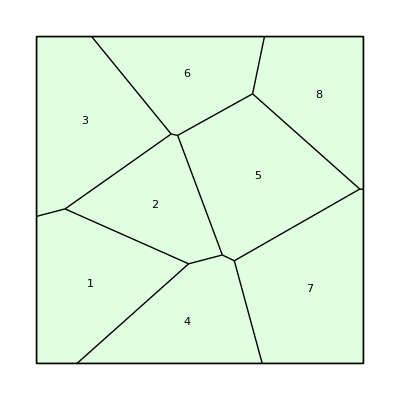

```mathematica
w=TemplateRandomSquareGrid[5,{0,0},{100,100}];
ShowTissue[w, "CellNumbers"->True]
```

```mathematica
CellNeighbors[w, 5]
```

{2,4,6,7,8}

```mathematica
CellNeighbors[w, 4]
```

{1,2,5,7}

```mathematica
CellNeighbors[w]
```

{{2,3,4},{1,3,4,5,6},{1,2,6},{1,2,5,7},{2,4,6,7,8},{2,3,5,8},{4,5,8},{5,6,7}}